## Practical 1 Ques nth root of unity geometric plot

```mathematica
n=7;
roots=ComplexExpand[z/.N[Solve[z^n-1==0]]];
pts={Re[#],Im[#]}&/@roots;
pts=SortBy[pts,ArcTan@@#&];
A1=Show[Graphics[{Red,Thick,Circle[{0,0},1]}],
ListLinePlot[Append[pts,First[pts]],PlotStyle->{Blue,Dashed,Thick},PlotMarkers->Automatic],
Axes->True,ImageSize->100,PlotLabel->"For n = 7"]
```

-Graphics-

## or

```mathematica
n=7;
roots=Exp[2Pi I Range[0,n-1]/n];
pts={Re[#],Im[#]}&/@roots;
A1=Show[Graphics[{Red,Thick,Circle[{0,0},1]}],
ListLinePlot[Append[pts,First[pts]],PlotStyle->{Blue,Dashed,Thick},PlotMarkers->Automatic],
Axes->True,ImageSize->100,PlotLabel->"For n = 7"]
```

-Graphics-

## Practical 2 Find solution of z^4=-625*I and represent solution geometrically .

```mathematica
sol=ComplexExpand[z/.Solve[z^4+625*I==0]]
pts={Re[#],Im[#]}&/@sol;
a=Graphics[{Red,Thick,Circle[{0,0},5]}];
b=Graphics[{Magenta,PointSize[Large],Point[pts]},ImageSize->100,Axes->True];
Show[b,a]
```

{5 Cos[π/8]-5 ⅈ Sin[π/8],-5 Cos[π/8]+5 ⅈ Sin[π/8],5 ⅈ Cos[π/8]+5 Sin[π/8],-5 ⅈ Cos[π/8]-5 Sin[π/8]}

-Graphics-

## Practical 3 Ques effect of rotation of ellipse by pi/6 radians and centre shifting from origin to (-1,1) using parametric plot, eqn is (cost,4sint)

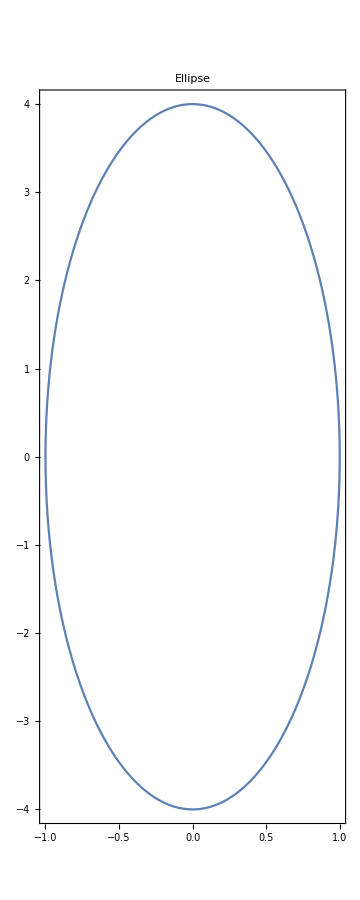
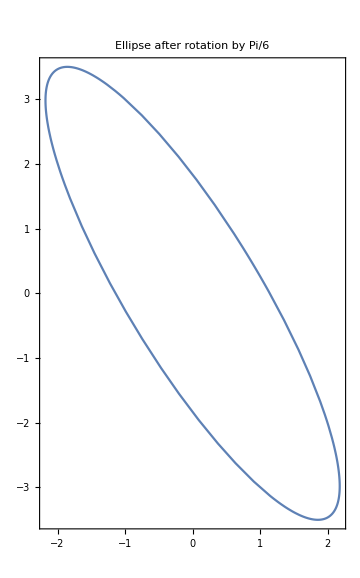
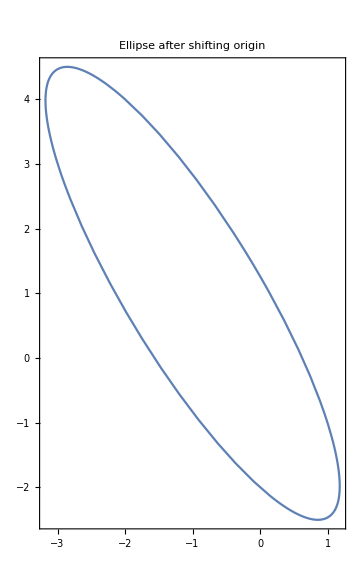

```mathematica
A1=ParametricPlot[{Cos[t],4Sin[t]},{t,0,2 Pi},Frame->True,ImageSize->Medium,PlotLabel->"Ellipse"];
A2=ParametricPlot[{Cos[t]Cos[Pi/6]-4Sin[t]Sin[Pi/6],Cos[t]Sin[Pi/6]+4Sin[t]Cos[Pi/6]},{t,0,2 Pi},Frame->True,ImageSize->Medium,PlotLabel->"Ellipse after rotation by Pi/6"];
A3=ParametricPlot[{Cos[t]Cos[Pi/6]-4Sin[t]Sin[Pi/6]-1,Cos[t]Sin[Pi/6]+4Sin[t]Cos[Pi/6]+1},{t,0,2 Pi},Frame->True,ImageSize->Medium,PlotLabel->"Ellipse after shifting origin"];
Print[A1,A2,A3]
```

## Practical 4 Show that the image of the open disk D1 (−1 − 𝑖) = {𝑧 : 𝑧 + 1 + 𝑖 < 1} under the linear transformation w = f (z) = (3–4 i) z + (6 + 2 i) is the open disk : D5 (–1 + 3 i) = {w : w + 1–3 i < 5}.

```mathematica
Solve[w1==(3-4I)z1+(6+2I),z1]
```

{{z1→1/25 (-10+3 w1+2 ⅈ (-15+2 w1))}}

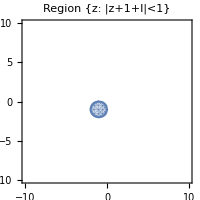
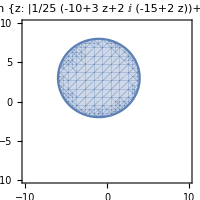

```mathematica
z=x+I*y;
A1=RegionPlot[Abs[z+1+I]<1,{x,-10,10},{y,-10,10},
Axes->True,ImageSize->200,PlotLabel->"Region {z: |z+1+I|<1}"];
A2=RegionPlot[Abs[1/25 (-10+3 z+2 I (-15+2 z))+1+I]<1,{x,-10,10},{y,-10,10},
Axes->True,ImageSize->200,PlotLabel->"Region {z: |1/25 (-10+3 z+2 ⅈ (-15+2 z))+1+I|<1}"];
Print[A1,A2]
```

## Practical 5

```mathematica
Solve[w1==(-1-I)z1-2+3I,z1]
```

{{z1→1/2 (1-w1+ⅈ (5+w1))}}

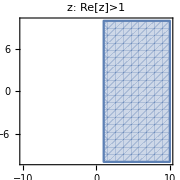
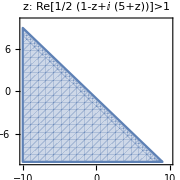

```mathematica
z=x+I*y;
A1=RegionPlot[Re[z]>1,{x,-10,10},{y,-10,10},Axes->True,ImageSize->Small,PlotLabel->"z: Re[z]>1"];
A2=RegionPlot[Re[1/2 (1-z+ⅈ (5+z))]>1,{x,-10,10},{y,-10,10},Axes->True,ImageSize->Small,PlotLabel->"z: Re[1/2 (1-z+ⅈ (5+z))]>1"];
Print[A1,A2]
```

## Practical 6 Same as 4 & 5

## Practical 7 Make a plot of the vertical lines x=a for a = -1, -1/2, 1/2, 1 and horizontal lines y = b for b = -1, -1/2, 1/2, 1. Find plot of this grid under mapping w = f[z]= 1/z.

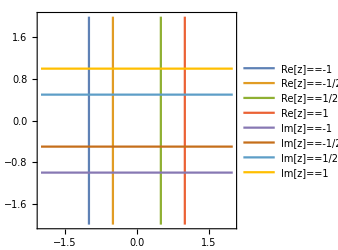
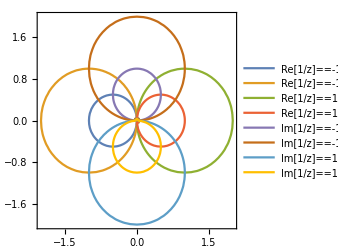

```mathematica
z=x+I*y;
A1=ContourPlot[{Re[z]==-1,Re[z]==-1/2,Re[z]==1/2,Re[z]==1,Im[z]==-1,Im[z]==-1/2,Im[z]==1/2,Im[z]==1},{x,-2,2},{y,-2,2},Axes->True,ImageSize->250,PlotLegends->{"Re[z]==-1","Re[z]==-1/2","Re[z]==1/2","Re[z]==1","Im[z]==-1","Im[z]==-1/2","Im[z]==1/2","Im[z]==1"}];
A2=ContourPlot[{Re[1/z]==-1,Re[1/z]==-1/2,Re[1/z]==1/2,Re[1/z]==1,Im[1/z]==-1,Im[1/z]==-1/2,Im[1/z]==1/2,Im[1/z]==1},{x,-2,2},{y,-2,2},Axes->True,ImageSize->250,PlotLegends->{"Re[1/z]==-1","Re[1/z]==-1/2","Re[1/z]==1/2","Re[1/z]==1","Im[1/z]==-1","Im[1/z]==-1/2","Im[1/z]==1/2","Im[1/z]==1"}];
Print[A1,A2]
```

## Practical 8 Find a parametric Representation of the path C = C1 + C2 + C3, FROM - 1 + I to 3 - I, where C1 is the line from - 1 + I to - 1; C2 is a line from - 1 to 1 + I and C 3 is a line from 1 + I to 3 - I. Make a plot of this path.

The Parametric representation of path C1,C2,C3 is given by

C1: z1[t]=(-1+ⅈ) (1-t)-t  0<=t<=1

C2: z2[t]=-1+(2+ⅈ) t  0<=t<=1

C3: z3[t]=(1+ⅈ) (1-t)+(3-ⅈ) t  0<=t<=1

The plot of the polynomial C= C1+C2+C3 is given by figure

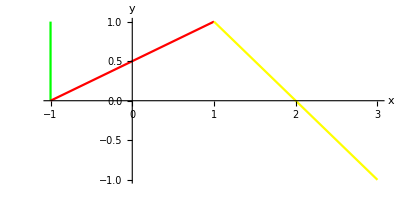

```mathematica
w1:=-1+I;
w2:=-1;
w3:=1+I;
w4:=3-I;
z1[t_]:=(1-t)w1+t w2;
z2[t_]:=(1-t)w2+t w3;
z3[t_]:=(1-t)w3+t w4;
Print["The Parametric representation of path C1,C2,C3 is given by"]
Print["C1: z1[t]=",z1[t],"  0<=t<=1"]
Print["C2: z2[t]=",z2[t],"  0<=t<=1"]
Print["C3: z3[t]=",z3[t],"  0<=t<=1"]
Print["The plot of the polynomial C= C1+C2+C3 is given by figure "]
ParametricPlot[{{Re[z1[t]],Im[z1[t]]},{Re[z2[t]],Im[z2[t]]},{Re[z3[t]],Im[z3[t]]}},{t,0,1},PlotStyle->{Green,Red,Yellow},AxesLabel->{"x","y"}]
```

## Practical 9 Find the line segment “L” joining the point A=0 to B=2+I (Pi/4), and give the exact calculation of Contour Integral e^z dz

The parametrization of line seqment l joining points A to B is (2+(ⅈ π)/4) t   0≤t≤1

The plot of line segment L is given by figure

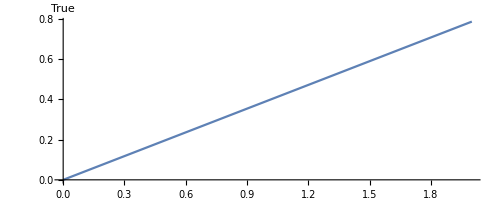

Value of Integral is -1+((1+ⅈ) ⅇ^2)/(√2)

```mathematica
a:=0;
b:=2+I*Pi/4;
z[t_]:=(1-t)a+t*b;
f[z_]:=Exp[z];
Print[" The parametrization of line seqment l joining points A to B is ",z[t],"   0≤t≤1"];
Print["The plot of line segment L is given by figure"];
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},AxesLabel->True]
Print["Value of Integral is ",ComplexExpand[Integrate[f[z[t]]*z'[t],{t,0,1}]]]
```

## Practical 10 Plot the semicircle’C’with the radius 1 at z = 2and evaluate the contour integral ∫c 1/(z-2)dz

```mathematica
Quit[]
```

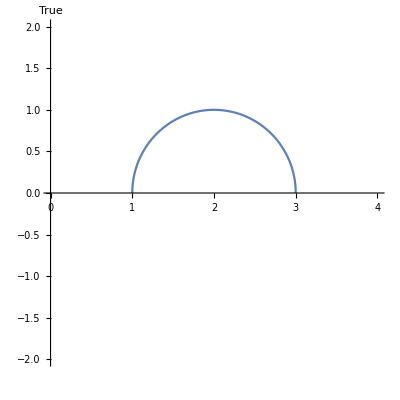

Value of Integral is ⅈ π

```mathematica
z[t_]:=2+Cos[t]+I*Sin[t];
f[z_]:=1/(z-2);
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,Pi},PlotRange->{{0,4},{-2,2}}, AxesLabel->True]
Print["Value of Integral is ",ComplexExpand[Integrate[f[z[t]]*z'[t],{t,0,Pi}]]]
```

## Practical 11 Show that ∫c1 zdz = ∫c2 zdz = 4 + 2*I, where C1 is the line segment from-1+I to 3+I, andC2 is the portion of parabola x = y^2 +2y joining -I to 3+I.Make plots of two contours C1 and C2 joining -1-I to 3+I.

The parametrization of the line segment C1 is given by

C1: z[t] = (-1-ⅈ) (1-t)+(3+ⅈ) t , 0<=t<=1

The parametrization of the portion of parabola C2 is given by

C2: z[t] = (2+ⅈ) t+t^2 ,-1<=t<=1

The plots of the line segment C1 and portion of the parabola C2 is given by the figure

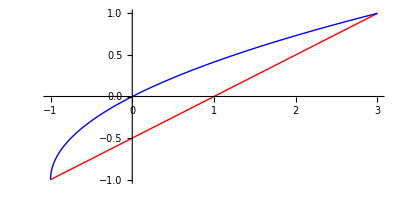

∫c1 zdz = 4+2 ⅈ------(1)

∫c2 zdz = 4+2 ⅈ------(2)

There by (1) and (2), we proved the required part.

```mathematica
w1:=-1-I;w2:=3+I;z1[t_]:=(1-t)*w1+t*w2;z2[t_]:=(t^2+2t)+I*t;Print["The parametrization of the line segment C1 is given by"]
Print["C1: z[t] = ",z1[t]," , 0<=t<=1"]
Print["The parametrization of the portion of parabola C2 is given by"]
Print["C2: z[t] = ",z2[t]," ,-1<=t<=1"]
Print["The plots of the line segment C1 and portion of the parabola C2 is given by the figure"]
Show[ParametricPlot[{Re[z1[t]],Im[z1[t]]},{t,0,1},PlotStyle->{Thick,Red}],ParametricPlot[{Re[z2[t]],Im[z2[t]]},{t,-1,1},PlotStyle->{Thick,Blue}]]
f[z_]:=z;
Print["∫c1 zdz = ",Integrate[f[z1[t]]*z1'[t],{t,0,1}],"------(1)"]
Print["∫c2 zdz = ",Integrate[f[z2[t]]*z2'[t],{t,-1,1}],"------(2)"]
Print["There by (1) and (2), we proved the required part."]
```

## Practical 12

```mathematica
Quit[]
```

The parametrization of the line segment C : 1+ⅈ t

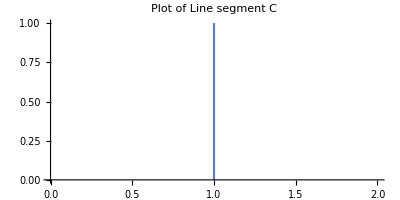

Thus by the ML inequality, upper bound of given integral is 2<=2√2

Hence the required inequality obtained

```mathematica
a:=1;
b:=1+I;
z[t_]:=(1-t)a+t*b;
f[z_]:=z^2;
Print["The parametrization of the line segment C : ",z[t]];
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotLabel->"Plot of Line segment C"]
L=Integrate[Abs[z'[t]],{t,0,1}];
r=ComplexExpand[Re[f[z[t]]]];
i=ComplexExpand[Im[f[z[t]]]];
M=Maximize[{(r^2+i^2)^(1/2),0≤t≤1},t];
ML=M[[1]]*L;
Print["Thus by the ML inequality, upper bound of given integral is ",ML,"<=2√2"]
Print["Hence the required inequality obtained"]
```

## Or

The parametrization equation of the given curve is C : z[t] = 2+ⅈ t Where 0<t⩽1, which represent straight line joining the points z0 = 2 and z1 = 2+ⅈ.

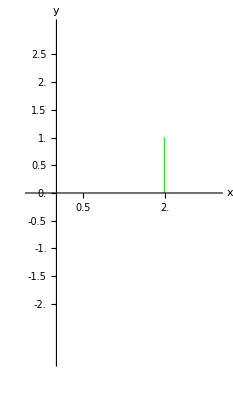

Length of the Arc is, L = 1 and the value of M is 1/5.

Using the ML Inequality, we have an upper bound for the given integral as 1/5.

```mathematica
z0=2;
z1=2+I;
z[t_]=z0+t*(z1-z0);
Print["The parametrization equation of the given curve is C : z[t] = ",ComplexExpand[z[t]]," Where 0<t⩽1, which represent straight line joining the points z0 = ",z0," and z1 = ",z1,"."]
p1=ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},AxesStyle->Arrowheads[{-0.03,0.03}],AxesLabel->{"x","y"},PlotStyle->{Thick,Green},AxesOrigin->{0,0},Ticks->{Range[-1,3,.5],Range[-2,2.5,0.5]},PlotRange->{{-0.5,3},{-3,3}}];
Show[p1]
L=Integrate[Abs[z'[t]],{t,0,1}];
f[z_]=1/(z^2+1);
r=ComplexExpand[Re[f[z[t]]]];
i=ComplexExpand[Im[f[z[t]]]];
M=Maximize[{(r^2+i^2)^(1/2),0≤t≤1},t];
ML=M[[1]]*L;
Print["Length of the Arc is, L = ",1," and the value of M is ",M[[1]],"."]
Print["Using the ML Inequality, we have an upper bound for the given integral as",ML,"."]
Manipulate[Show[ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->{Thick,Red},PlotRange->2],ListLinePlot[{{{0,1},{Re[z[t]],Im[z[t]]}},{{0,-1},{Re[z[t]],Im[z[t]]}}},AxesOrigin->{0,0}]],{t,0,1}]
```

## Practical 13 Find and plot three Laurant Series representation for the function f[z]= 3/(2+z- z^2) involving powers of z.

Laurent Series around z=0 : 3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+(513 z^8)/512-(1023 z^9)/1024+(2049 z^10)/2048

Laurent Series around z=2 : 1/3+(2-z)/9-1/(-2+z)+1/27 (-2+z)^2-1/81 (-2+z)^3+1/243 (-2+z)^4-1/729 (-2+z)^5+(-2+z)^6/2187-(-2+z)^7/6561+(-2+z)^8/19683-(-2+z)^9/59049+(-2+z)^10/177147

Laurent Series around z=Infinity : -513/z^10-255/z^9-129/z^8-63/z^7-33/z^6-15/z^5-9/z^4-3/z^3-3/z^2

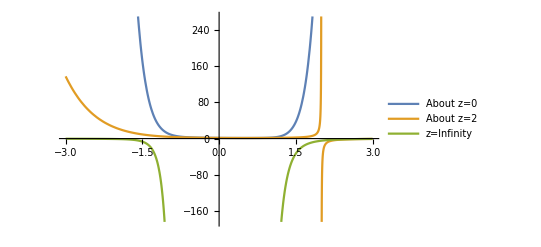

```mathematica
f[z_]:=3/(2+z-z^2);
s1=Normal[Series[f[z],{z,0,10}]];
s2=Normal[Series[f[z],{z,2,10}]];
s3=Normal[Series[f[z],{z,Infinity,10}]];
Print["Laurent Series around z=0 : ",s1];
Print["Laurent Series around z=2 : ",s2];
Print["Laurent Series around z=Infinity : ",s3];
Plot[{s1,s2,s3},{z,-3,3},PlotLegends->{"About z=0","About z=2","z=Infinity"}]
```

## Practical 14 Locate the poles of f[z] = 1/(5z^4 + 26 z^2 + 5)

```mathematica
f[z_]:=1/(5 z^4+26 z^2+5);
sol=Solve[Denominator[f[z]]==0,z];
a=z/.sol;
Print["Poles are z1=",a[[1]],",z2=",a[[2]],", z3=",a[[3]]," & z4 = ",a[[4]]]
```

Poles are z1=-ⅈ/(√5),z2=ⅈ/(√5), z3=-ⅈ √5 & z4 = ⅈ √5

## Practical 15 Locate the poles and zeroes of g[z] = πCot[πz]/z^2, Determine their order, also justify that Res(g,θ)=- -(π^2)/3

```mathematica
g[z_]:=(Pi*Cot[Pi*z])/z^2;
pole=Solve[Denominator[g[z]]==0,z];
zero=Reduce[g[z]==0,z];
res=Residue[g[z],{z,0}];
Print["Poles are  ",pole];
Print["zeroes are   ",zero];
Print["Residue of g[z] at z=0 is ",res]
```

Poles are  {{z→0},{z→0}}

zeroes are   C[1]∈ℤ&&z≠0&&z==(π/2+π C[1])/π

Residue of g[z] at z=0 is -π^2/3

## Practical 16 Evaluate ∫c1(θ) e^(2/z) dz , where c1(0) denotes the circle {z : |z|=1} with positive orientation. Similarly evaluate ∫_c1 1/(z^4+z^3-2 z^2)ⅆz.

```mathematica
g[z_]:=1/(z^4+z^3-2 z^2);
Apart[g[z]]
```

1/(3 (-1+z))-1/(2 z^2)-1/(4 z)-1/(12 (2+z))

```mathematica
r1=SeriesCoefficient[g[z],{z,0,-1}];
r2=SeriesCoefficient[g[z],{z,1,-1}];
r3=SeriesCoefficient[g[z],{z,-2,-1}];
Print[" The residue of g[z] at z = 0 is ",r1," , at z = 1 is ",r2," & at z = -2 is ", r3];
integral=2 Pi I*(r1+r2+r3);
Print["The value of∫_c1 1/z^4ⅆz by Cauchy residue theorem is ",integral]
```

The residue of g[z] at z = 0 is -1/4 , at z = 1 is 1/3 & at z = -2 is -1/12

The value of∫_c1 1/z^4ⅆz by Cauchy residue theorem is 0